```mathematica
Together[ExpandAll[(ⅇ^(ⅈ ω)-.3)/(ⅇ^(ⅈ ω)-.5)(ⅇ^(-ⅈ ω)-.3)/(ⅇ^(-ⅈ ω)-.5)]]
```

(-0.3+1.09 ⅇ^(ⅈ ω)-0.3 ⅇ^(2 ⅈ ω))/(-0.5+1.25 ⅇ^(ⅈ ω)-0.5 ⅇ^(2 ⅈ ω))

```mathematica
Simplify[(10 ⅇ^(ⅈ ω)-3)/(10 ⅇ^(ⅈ ω)-5)(10 ⅇ^(-ⅈ ω)-3)/(10 ⅇ^(-ⅈ ω)-5)]
```

(30-109 ⅇ^(ⅈ ω)+30 ⅇ^(2 ⅈ ω))/(50-125 ⅇ^(ⅈ ω)+50 ⅇ^(2 ⅈ ω))

```mathematica
FullSimplify[(10 ⅇ^(ⅈ ω)-3)/(10 ⅇ^(ⅈ ω)-5)(10 ⅇ^(-ⅈ ω)-3)/(10 ⅇ^(-ⅈ ω)-5)]
```

3/5-34/(25 (-5+4 Cos[ω]))

```mathematica
TrigToExp[Cos[ω]]
```

ⅇ^(-ⅈ ω)/2+ⅇ^(ⅈ ω)/2

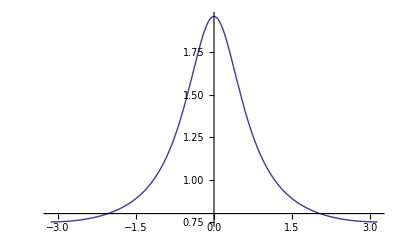

```mathematica
Plot[(10 ⅇ^(ⅈ ω)-3)/(10 ⅇ^(ⅈ ω)-5)(10 ⅇ^(-ⅈ ω)-3)/(10 ⅇ^(-ⅈ ω)-5),{ω,-π,π}]
```

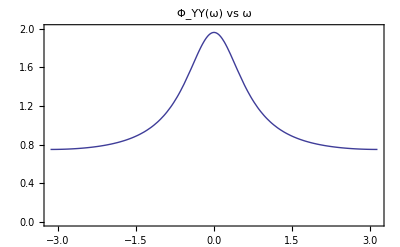

```mathematica
Plot[Abs[(ⅇ^(ⅈ ω)-0.3)/(ⅇ^(ⅈ ω)-0.5)]^2,{ω,-π,π},PlotRange->{0,2},Frame->True,PlotLabel->"Φ_YY(ω) vs ω"]
```

```mathematica
Simplify[Together[(A z)/(z-1/2)+B+(A/z)/(1/z-1/2)+B]]
```

(2 (A (1-4 z+z^2)+B (2-5 z+2 z^2)))/(2-5 z+2 z^2)

```mathematica
Simplify[Together[(A z)/(z-0.5)+B+(A/z)/(1/z-0.5)+B]]
```

(-1. B (-2.+z) (-0.5+z)-0.5 A (-3.73205+z) (-0.267949+z))/((1.-0.5 z) (-0.5+z))

```mathematica
Expand[(1/z-0.5)(z-0.5)]
```

1.25-0.5/z-0.5 z

```mathematica
Apart[0.34/(1.25-0.5z-0.5/z)]
```

-0.906667/(-2.+z)+0.226667/(-0.5+z)

```mathematica
Expand[A z(1/z-0.5)+2B(1/z-0.5)(z-0.5)+A(z-0.5)/z]
```

2 A+2.5 B-(0.5 A)/z-(1. B)/z-0.5 A z-1. B z

```mathematica
1.09-2.5 0.3
```

0.34

```mathematica
0.3-0.25 1.09
```

0.0275

```mathematica
(1.09-2.5 0.3)/(2-2.5 0.5)
```

0.453333

```mathematica
1-0.25 2.5
```

0.375

```mathematica
(0.3-0.25 1.09)/(1-0.25 2.5)
```

0.0733333

```mathematica
InverseZTransform[A z/(z-c),z,k]
```

A c^k

```mathematica
Solve[{2A+2.5B==1.09,0.5A+B==0.3}]
```

{{A→0.453333,B→0.0733333}}

```mathematica
2A+2B/.Solve[{2A+2.5B==1.09,0.5A+B==0.3}]
```

{1.05333}

```mathematica
Solve[{ΛYW0-ΛYW1/2==1,ΛYW1-ΛYW0/2==3/10}]
```

{{ΛYW0→23/15,ΛYW1→16/15}}

```mathematica
Solve[{ΛYW0-ΛYW1/2==1,ΛYW1-ΛYW0/2==3/10}]//N
```

{{ΛYW0→1.53333,ΛYW1→1.06667}}

```mathematica
Expand[yk^2==(ykm1/2+wk-3wkm1/10)^2]
```

yk^2==wk^2-(3 wk wkm1)/5+(9 wkm1^2)/100+wk ykm1-(3 wkm1 ykm1)/10+ykm1^2/4

```mathematica
Expand[yk^2==(ykm1/2+wk-3wkm1/10)^2]/.{wk^2->1,wk wkm1->0,wkm1^2->1,wk ykm1->0,wkm1 ykm1->1}
```

yk^2==79/100+ykm1^2/4

```mathematica
.79 4/3
```

1.05333

```mathematica
Assuming[x∈Reals,Simplify[Sqrt[x^2]]]
```

Abs[x]

```mathematica
(w^2/4+1)/(w^4+5 w^2+1)/.w->-I s
```

(1-s^2/4)/(1-5 s^2+s^4)

```mathematica
G[w_]=(b1 w+b2)/(w^2+a1 w+a2);
```

```mathematica
Expand[Numerator[G[I w]G[-I w]]]
Expand[Denominator[G[I w]G[-I w]]]
```

b2^2+b1^2 w^2

a2^2+a1^2 w^2-2 a2 w^2+w^4

```mathematica
Expand[Numerator[G[-I s]G[-I s]]]
Expand[Denominator[G[-I s]G[-I s]]]
```

b2^2-2 ⅈ b1 b2 s-b1^2 s^2

a3^2-2 ⅈ a2 a3 s-a2^2 s^2-2 a1 a3 s^2+2 ⅈ a1 a2 s^3+a1^2 s^4

```mathematica
(b1 I(-I s)+b2)/(a1 (-I s)^2+a2 I(-I s)+a3)/.Solve[Reduce[{((-b1 I I>0&&b2>0)||(-b1 I I<0&&b2<0))&&((a1(-I)^2>0&&-a2 I I>0&&a3>0)||(a1(-I)^2<0&&-a2 I I<0&&a3<0))&&b2^2==1&&-(b1 I)^2==1/4&&a3^2==1&&-(a2 I)^2+2 a1 a3 ==5&&a1^2==1}]]
```

{(-1-s/2)/(1+√7 s+s^2),(-1-s/2)/(-1-√7 s-s^2),(1+s/2)/(1+√7 s+s^2),(1+s/2)/(-1-√7 s-s^2)}

```mathematica
Solve[{b2^2==1,-b1^2==1/4,a3^2==1,-a2^2+2 a1 a3 ==5,a1^2==1}]
```

{{b2→-1,a1→-1,a3→-1,a2→-ⅈ √3,b1→-ⅈ/2},{b2→-1,a1→-1,a3→-1,a2→-ⅈ √3,b1→ⅈ/2},{b2→-1,a1→-1,a3→-1,a2→ⅈ √3,b1→-ⅈ/2},{b2→-1,a1→-1,a3→-1,a2→ⅈ √3,b1→ⅈ/2},{b2→-1,a1→-1,a3→1,a2→-ⅈ √7,b1→-ⅈ/2},{b2→-1,a1→-1,a3→1,a2→-ⅈ √7,b1→ⅈ/2},{b2→-1,a1→-1,a3→1,a2→ⅈ √7,b1→-ⅈ/2},{b2→-1,a1→-1,a3→1,a2→ⅈ √7,b1→ⅈ/2},{b2→-1,a1→1,a3→-1,a2→-ⅈ √7,b1→-ⅈ/2},{b2→-1,a1→1,a3→-1,a2→-ⅈ √7,b1→ⅈ/2},{b2→-1,a1→1,a3→-1,a2→ⅈ √7,b1→-ⅈ/2},{b2→-1,a1→1,a3→-1,a2→ⅈ √7,b1→ⅈ/2},{b2→-1,a1→1,a3→1,a2→-ⅈ √3,b1→-ⅈ/2},{b2→-1,a1→1,a3→1,a2→-ⅈ √3,b1→ⅈ/2},{b2→-1,a1→1,a3→1,a2→ⅈ √3,b1→-ⅈ/2},{b2→-1,a1→1,a3→1,a2→ⅈ √3,b1→ⅈ/2},{b2→1,a1→-1,a3→-1,a2→-ⅈ √3,b1→-ⅈ/2},{b2→1,a1→-1,a3→-1,a2→-ⅈ √3,b1→ⅈ/2},{b2→1,a1→-1,a3→-1,a2→ⅈ √3,b1→-ⅈ/2},{b2→1,a1→-1,a3→-1,a2→ⅈ √3,b1→ⅈ/2},{b2→1,a1→-1,a3→1,a2→-ⅈ √7,b1→-ⅈ/2},{b2→1,a1→-1,a3→1,a2→-ⅈ √7,b1→ⅈ/2},{b2→1,a1→-1,a3→1,a2→ⅈ √7,b1→-ⅈ/2},{b2→1,a1→-1,a3→1,a2→ⅈ √7,b1→ⅈ/2},{b2→1,a1→1,a3→-1,a2→-ⅈ √7,b1→-ⅈ/2},{b2→1,a1→1,a3→-1,a2→-ⅈ √7,b1→ⅈ/2},{b2→1,a1→1,a3→-1,a2→ⅈ √7,b1→-ⅈ/2},{b2→1,a1→1,a3→-1,a2→ⅈ √7,b1→ⅈ/2},{b2→1,a1→1,a3→1,a2→-ⅈ √3,b1→-ⅈ/2},{b2→1,a1→1,a3→1,a2→-ⅈ √3,b1→ⅈ/2},{b2→1,a1→1,a3→1,a2→ⅈ √3,b1→-ⅈ/2},{b2→1,a1→1,a3→1,a2→ⅈ √3,b1→ⅈ/2}}

```mathematica
(SameQ@@#&/@Sign[CoefficientList[Numerator[Simplify[G[-I s]/.Solve[{b2^2==1,-b1^2==1/4,a3^2==1,-a2^2+2 a1 a3 ==5,a1^2==1}]]],s]])
```

{True,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,False,True,False,True,False,True,False,True,False,True,False,True,False,True,False,True}

```mathematica
Thread[(SameQ@@#&/@Sign[CoefficientList[Numerator[Simplify[G[-I s]/.Solve[{b2^2==1,-b1^2==1/4,a3^2==1,-a2^2+2 a1 a3 ==5,a1^2==1}]]],s]])&&(SameQ@@#&/@Sign[CoefficientList[Denominator[Simplify[G[-I s]/.Solve[{b2^2==1,-b1^2==1/4,a3^2==1,-a2^2+2 a1 a3 ==5,a1^2==1}]]],s]])]
```

{False,False,False,False,False,False,True,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,True,False,False,False,False,False,False}

```mathematica
Simplify[Reduce[{Real[-(ⅈ b2)/b1]≤0,Real[-(ⅈ a2-√(-a2^2+4 a1 a3))/(2 a1)]≤0,Real[-(ⅈ a2+√(-a2^2+4 a1 a3))/(2 a1)]≤0,b2^2==1,-b1^2==1/4,a3^2==1,-a2^2+2 a1 a3 ==5,a1^2==1}]]
```

(Real[(-ⅈ a2+√(-a2^2+4 a1 a3))/(2 a1)]|Real[-(ⅈ a2+√(-a2^2+4 a1 a3))/(2 a1)]|Real[-(ⅈ b2)/b1])∈Reals&&(b1==-ⅈ/2||b1==ⅈ/2)&&(1+b2==0||b2==1)&&((1+a1==0&&((1+a3==0&&(a2==-ⅈ √3||a2==ⅈ √3))||(a3==1&&(a2==-ⅈ √7||a2==ⅈ √7))))||(a1==1&&((a3==1&&(a2==-ⅈ √3||a2==ⅈ √3))||(1+a3==0&&(a2==-ⅈ √7||a2==ⅈ √7)))))

```mathematica
Simplify[RSolve[{X[k+1]==A X[k]+B,X[0]==X0},X[k],k]]
```

{{X[k]→((-1+A^k) B+(-1+A) A^k X0)/(-1+A)}}

```mathematica
1.672Inverse[IdentityMatrix[2]-{{-8/100,-1},{7/10,1/10}}]
```

{{0.9,-1.},{0.7,1.08}}

```mathematica
1.672Inverse[IdentityMatrix[2]-{{-8/100,-1},{7/10,1/10}}].{0.34,0.3}
```

{0.006,0.562}

```mathematica
1.08 0.9+0.7
```

1.672

```mathematica
0.7 0.34+1.08 0.3
```

0.562

```mathematica
0.7 0.34+0.08 0.3
```

0.262

```mathematica
3 0.562 10/1.672
```

10.0837

```mathematica
Inverse[{{-0.08,-1},{0.7,0.1}}]
```

{{0.144509,1.44509},{-1.01156,-0.115607}}

```mathematica
Limit[MatrixPower[{{-0.08,-1},{0.7,0.1}},k],k->∞]
```

{{0.,0.},{0.,0.}}

```mathematica
{{0,3}}.Inverse[IdentityMatrix[2]-{{-8/100,-1},{7/10,1/10}}].{0.34,0.3}10
```

{10.0837}

```mathematica
CoefficientList[#,z]&/@{Numerator[#],Denominator[#]}&[Together[({{0,3}}.Inverse[z IdentityMatrix[2]-{{-8/100,-1},{7/10,1/10}}].{34/100,3/10})({{0,3}}.Inverse[1/z IdentityMatrix[2]-{{-8/100,-1},{7/10,1/10}}].{34/100,3/10})]]0.692/173000
```

{{{0,0.7074,1.4278,0.7074}},{{0.692,-0.03384,1.47926,-0.03384,0.692}}}

```mathematica
Expand[{Numerator[#],Denominator[#]}&[FullSimplify[({{0,3}}.Inverse[ⅇ^(ⅉ ω) IdentityMatrix[2]-{{-8/100,-1},{7/10,1/10}}].{34/100,3/10})({{0,3}}.Inverse[ⅇ^(-ⅉ ω) IdentityMatrix[2]-{{-8/100,-1},{7/10,1/10}}].{34/100,3/10})]]0.692/(4 43250)]
```

{{1.4278+1.4148 Cos[ω]},{1.47926-0.06768 Cos[ω]+1.384 Cos[2 ω]}}

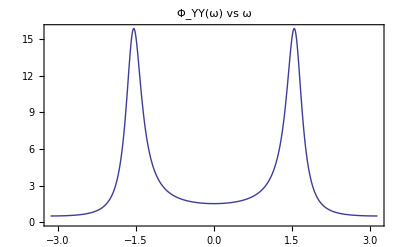

```mathematica
Plot[FullSimplify[({{0,3}}.Inverse[ⅇ^(ⅉ ω) IdentityMatrix[2]-{{-8/100,-1},{7/10,1/10}}].{34/100,3/10})({{0,3}}.Inverse[ⅇ^(-ⅉ ω) IdentityMatrix[2]-{{-8/100,-1},{7/10,1/10}}].{34/100,3/10})]+1/2,{ω,-Pi,Pi},Frame->True,PlotLabel->"Φ_YY(ω) vs ω"]
```

```mathematica
FullSimplify[RSolve[{X[k+1]==A X[k]+B W[k],X[k0]==Xk0},X[k],k]]
```

{{X[k]→A^(k-k0) Xk0+A^(-1+k) (∑_(K[1]=0)^(-1+k) A^(-K[1]) B W[K[1]]-∑_(K[1]=0)^(-1+k0) A^(-K[1]) B W[K[1]])}}

```mathematica
Simplify[X[k+5]/.{X->(A X[#-1]+B W[#-1]&)}/.{X->(A X[#-1]+B W[#-1]&)}/.{X->(A X[#-1]+B W[#-1]&)}/.{X->(A X[#-1]+B W[#-1]&)}/.{X->(A X[#-1]+B W[#-1]&)}]
```

A^4 B W[k]+A^3 B W[1+k]+A^2 B W[2+k]+A B W[3+k]+B W[4+k]+A^5 X[k]

```mathematica
FullSimplify[X[k+5]/.{X->(mx[#]+A(X[#-1]-mx[#-1])+B(W[#-1]-mw)&)}/.{X->(mx[#]+A(X[#-1]-mx[#-1])+B(W[#-1]-mw)&)}/.{X->(mx[#]+A(X[#-1]-mx[#-1])+B(W[#-1]-mw)&)}/.{X->(mx[#]+A(X[#-1]-mx[#-1])+B(W[#-1]-mw)&)}/.{X->(mx[#]+A(X[#-1]-mx[#-1])+B(W[#-1]-mw)&)}]
```

-A^5 mx[k]+mx[5+k]+B (-(1+A+A^2+A^3+A^4) mw+A (A (A (A W[k]+W[1+k])+W[2+k])+W[3+k])+W[4+k])+A^5 X[k]

```mathematica
FullSimplify[mx[k+5]+A^5(X[k]-mx[k])+∑_(i=k)^(k+5-1) A^(k+5-1-i)B(W[i]-mw)]
```

-A^5 mx[k]+mx[5+k]+B (-(1+A+A^2+A^3+A^4) mw+A (A (A (A W[k]+W[1+k])+W[2+k])+W[3+k])+W[4+k])+A^5 X[k]

```mathematica
FullSimplify[mx[k+5]+A^5(X[k]-mx[k])+∑_(i=0)^(5-1) A^(5-1-i)B(W[k+i]-mw)]
```

-A^5 mx[k]+mx[5+k]+B (-(1+A+A^2+A^3+A^4) mw+A (A (A (A W[k]+W[1+k])+W[2+k])+W[3+k])+W[4+k])+A^5 X[k]

```mathematica
FullSimplify[(IdentityMatrix[2]-MatrixPower[{{a,b},{c,d}},k]).Inverse[IdentityMatrix[2]-{{a,b},{c,d}}]]
```

{{-1/(-1+a+b c+d-a d)((2^-k b c ((a-√(4 b c+(a-d)^2)+d)^k-(a+√(4 b c+(a-d)^2)+d)^k))/(√(4 b c+(a-d)^2))+1/2 (1-d) (2-(2^-k (a-√(4 b c+(a-d)^2)+d)^k (-a+√(4 b c+(a-d)^2)+d))/(√(4 b c+(a-d)^2))-(2^-k (a+√(4 b c+(a-d)^2)-d) (a+√(4 b c+(a-d)^2)+d)^k)/(√(4 b c+(a-d)^2)))),(2^(-1-k) b (-2^(1+k) √(4 b c+(a-d)^2)+√(4 b c+(a-d)^2) (a-√(4 b c+(a-d)^2)+d)^k+(-2+a+d) (a-√(4 b c+(a-d)^2)+d)^k+√(4 b c+(a-d)^2) (a+√(4 b c+(a-d)^2)+d)^k-(-2+a+d) (a+√(4 b c+(a-d)^2)+d)^k))/(√(4 b c+(a-d)^2) (-1+a+b c+d-a d))},{(2^(-1-k) c (-2^(1+k) √(4 b c+(a-d)^2)+√(4 b c+(a-d)^2) (a-√(4 b c+(a-d)^2)+d)^k+(-2+a+d) (a-√(4 b c+(a-d)^2)+d)^k+√(4 b c+(a-d)^2) (a+√(4 b c+(a-d)^2)+d)^k-(-2+a+d) (a+√(4 b c+(a-d)^2)+d)^k))/(√(4 b c+(a-d)^2) (-1+a+b c+d-a d)),-1/(-1+a+b c+d-a d)((2^-k b c ((a-√(4 b c+(a-d)^2)+d)^k-(a+√(4 b c+(a-d)^2)+d)^k))/(√(4 b c+(a-d)^2))+1/2 (1-a) (2-(2^-k (a+√(4 b c+(a-d)^2)-d) (a-√(4 b c+(a-d)^2)+d)^k)/(√(4 b c+(a-d)^2))-(2^-k (-a+√(4 b c+(a-d)^2)+d) (a+√(4 b c+(a-d)^2)+d)^k)/(√(4 b c+(a-d)^2))))}}

```mathematica
Inverse[{{z-a,-b},{-c,z-d}}]
∑_(z=-∞)^∞ %
```

{{(-d+z)/(-b c+a d-a z-d z+z^2),b/(-b c+a d-a z-d z+z^2)},{c/(-b c+a d-a z-d z+z^2),(-a+z)/(-b c+a d-a z-d z+z^2)}}

Sum::div: Sum does not converge.

General::stop: Further output of Sum will be suppressed during this calculation.

{{∑_(z=-∞)^∞ (-d+z)/(-b c+a d-a z-d z+z^2),-(b (PolyGamma[0,-a/2-d/2-1/2 √(a^2+4 b c-2 a d+d^2)]-PolyGamma[0,-a/2-d/2+1/2 √(a^2+4 b c-2 a d+d^2)]))/(√(a^2+4 b c-2 a d+d^2))-(b (PolyGamma[0,1+a/2+d/2-1/2 √(a^2+4 b c-2 a d+d^2)]-PolyGamma[0,1+a/2+d/2+1/2 √(a^2+4 b c-2 a d+d^2)]))/(√(a^2+4 b c-2 a d+d^2))},{-(c (PolyGamma[0,-a/2-d/2-1/2 √(a^2+4 b c-2 a d+d^2)]-PolyGamma[0,-a/2-d/2+1/2 √(a^2+4 b c-2 a d+d^2)]))/(√(a^2+4 b c-2 a d+d^2))-(c (PolyGamma[0,1+a/2+d/2-1/2 √(a^2+4 b c-2 a d+d^2)]-PolyGamma[0,1+a/2+d/2+1/2 √(a^2+4 b c-2 a d+d^2)]))/(√(a^2+4 b c-2 a d+d^2)),∑_(z=-∞)^∞ (-a+z)/(-b c+a d-a z-d z+z^2)}}

```mathematica
Expand[DSolve[{X'[t]==(a-L)X[t]+bw W[t]-L V[t],X[0]==X0},X[t],t]]
```

{{X[t]→ⅇ^((a-L) t) X0-ⅇ^((a-L) t) ∫_1^0 ⅇ^(-(a-L) K[1]) (-L V[K[1]]+bw W[K[1]])ⅆK[1]+ⅇ^((a-L) t) ∫_1^t ⅇ^(-(a-L) K[1]) (-L V[K[1]]+bw W[K[1]])ⅆK[1]}}

```mathematica
∫_0^t ⅇ^((a-L)(t-τ))ⅆτ
```

(-1+ⅇ^((a-L) t))/(a-L)

```mathematica
D[(b^2 sw^2+L^2 sv^2)/(2(a-L)^2), L]
```

(L sv^2)/(a-L)^2+(L^2 sv^2+b^2 sw^2)/(a-L)^3

```mathematica
Solve[D[(b^2 sw^2+L^2 sv^2)/(2(a-L)^2), L]==0,L]
```

{{L→-(b^2 sw^2)/(a sv^2)}}

```mathematica
FullSimplify[D[D[(b^2 sw^2+L^2 sv^2)/(2(a-L)^2), L], L]]
```

(a (a+2 L) sv^2+3 b^2 sw^2)/(a-L)^4

```mathematica
FullSimplify[D[D[(b^2 sw^2+L^2 sv^2)/(2(a-L)^2), L], L]/.Solve[D[(b^2 sw^2+L^2 sv^2)/(2(a-L)^2), L]==0,L]]
```

{(a^4 sv^8)/((a^2 sv^2+b^2 sw^2)^3)}

```mathematica
FullSimplify[(b^2 sw^2+L^2 sv^2)/(2(a-L)^2)/.Solve[D[(b^2 sw^2+L^2 sv^2)/(2(a-L)^2), L]==0,L]]
```

{(b^2 sv^2 sw^2)/(2 a^2 sv^2+2 b^2 sw^2)}

```mathematica
n=5;
Simplify[(Y[k]-∑_(i=1)^n a[i]Y[k-i])^2==(Y[k]^2-2∑_(i=1)^n a[i]Y[k]Y[k-i]+∑_(i=1)^n (a[i]Y[k-i]∑_(j=1)^n (a[j]Y[k-j])))]
Simplify[(Y[k]-∑_(i=1)^n a[i]Y[k-i])^2==(Y[k]^2-2∑_(i=1)^n a[i]Y[k]Y[k-i]+∑_(i=1)^n ∑_(j=1)^n (a[i]Y[k-i]a[j]Y[k-j]))]
k=3;
s[j_]=σ[Abs[j]];
Simplify[D[(s[0]-2∑_(i=1)^n a[i]s[i]+∑_(i=1)^n ∑_(j=1)^n (a[i]a[j]s[j-i])), a[k]]==(-2s[k]+∑_(j=1)^n 2a[j]s[j-k])]
```

True

True

True